# Calculation of the Point Spread Function from the Electromagnetic Theory of Diffraction

Abhishek Sharma
BioMIP
Ruhr Universität, Bochum

This work is part of publication of design of high speed fluorescence imaging microscopy optimized for microfluidic applications. In this Mathematica file, we calculate the point spread function of confocal microscopy with point illumination. These calculations are based on the following reference,

→ Antonin Miks, Jiri Novak, Pavel Novak, Calculation of point  spread function for optical systems with finite value of numerical aperture, Optik 118 (2007) 537–543

## Calculation of point spread function for point illumination

```mathematica
n1=1.0002;
n2 = 1.0002; m=4;
NA =1.3;
u2max = (1/(2NA));
M=(n2/n1 m)^2;
```

```mathematica
(* calculating the coefficients A0,A1...A5 for the calculations of the Complex Field fromt the series expansion *)
a0=1;a1=(1/4);a2=(5/32);a3=(15/128);a4=(195/2048);a5=(663/8192);
A0 = 1;
A1 =a1(1+M);
A2 =a2(1+ M^2) + (a1^2)M;
A3 =a3(1+ M^3) + a1 a2 M(1+M);
A4 =a4(1+ M^4) + a1 a3 M(1+M^2)+a2^2 M^2; 
A5= a5(1+ M^5) + a1 a4 M(1+M^2)+ a2 a3 M^2(1+M);

C0=(A0(Sin[u2max])^(2*k))/.k-> 0;
C1=(A1(Sin[u2max])^(2*1));
C2=(A2(Sin[u2max])^(2*2));
C3=(A3(Sin[u2max])^(2*3));
C4=(A4(Sin[u2max])^(2*4));
C5=(A5(Sin[u2max])^(2*5));
```

```mathematica
(* Using the Bessel Functions of the First Kind: Directly using the Solutions *)
InteG0[τ_]:=(1/τ)BesselJ[1,τ];
InteG1[τ_]:=(1/τ)BesselJ[1,τ] - (2/(τ^2))BesselJ[2,τ];
InteG2[τ_]:=(1/τ)BesselJ[1,τ] - (4/(τ^2))BesselJ[2,τ] + (8/(τ^3))BesselJ[3,τ];  
InteG3[τ_] := (1/τ)BesselJ[1,τ] - (6/(τ^2))BesselJ[2,τ] + (24/(τ^3))BesselJ[3,τ] -(48/(τ^4))BesselJ[4,τ];
InteG4[τ_] := (1/τ)BesselJ[1,τ] - (8/(τ^2))BesselJ[2,τ] + (48/(τ^3))BesselJ[3,τ] -(192/(τ^4))BesselJ[4,τ] + (384/(τ^5))BesselJ[5,τ];
InteG5[τ_] := (1/τ)BesselJ[1,τ] - (10/(τ^2))BesselJ[2,τ] + (80/(τ^3))BesselJ[3,τ] -(480/(τ^4))BesselJ[4,τ] + (1920/(τ^5))BesselJ[5,τ] -(3840/(τ^6))BesselJ[6,τ];
```

```mathematica
U[τ_]:= C0 InteG0[τ]+C1 InteG1[τ]+C2 InteG2[τ]+C3 InteG3[τ]+C4 InteG4[τ]+C5 InteG5[τ];
```

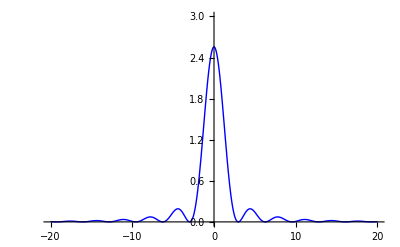

```mathematica
Plot[(U[τ])^2,{τ,-20,20},PlotRange-> {0,3},PlotStyle-> {Blue, Thick}]
```

```mathematica
PSF[x_,y_]:= U[ρ]/.ρ-> √(x^2+y^2)
GraphicsColumn[{Plot[(U[ρ])^2,{ρ,-20,20},PlotRange-> {0,3},PlotStyle-> {Blue,Thick}],Plot3D[(PSF[x,y])^2,{x,-10,10},{y,-10,10},PlotRange->{0,3}]},Frame-> All]
```

-Graphics-